```mathematica
(* Jai Prasadh
PHY 315
HW6
*)
a = 0.6 ;
B = 142(10^3);
s0 = 6.34(10^-7);
ρ=1.275 (* kg/m^3 *);
v = (B/ρ)^0.5;

s[x_,t_]:= (s0 (x-v t) a)/(a^2 + (x-v t)^2)
p[x_,t_]:=-B(s0)((a (a^2+(x-v t)^2)-2 (x-v t) (a (x-v t)))/(a^2+(x-v t)^2)^2)
```

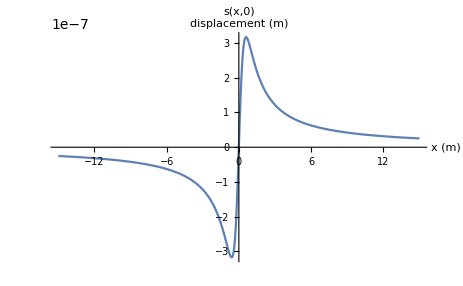

```mathematica
(* 1b *)
Plot[s[x,0],{x,-15,15},PlotLabel->"s(x,0)",AxesLabel->{"x (m)","displacement (m)"}]
```

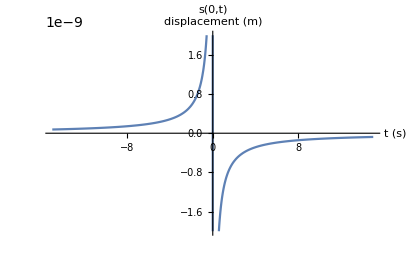

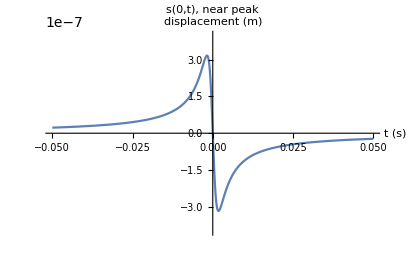

```mathematica
(* 1c *)
Plot[s[0,t],{t,-15,15},PlotRange->{-2(10^-9),2(10^-9)},PlotLabel->"s(0,t)",AxesLabel->{"t (s)","displacement (m)"}]
Plot[s[0,t],{t,-0.05,0.05},PlotRange->{-4(10^-7),4(10^-7)},PlotLabel->"s(0,t), near peak",AxesLabel->{"t (s)","displacement (m)"}]
```

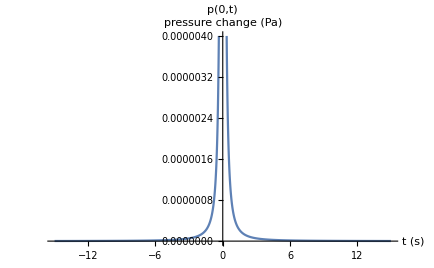

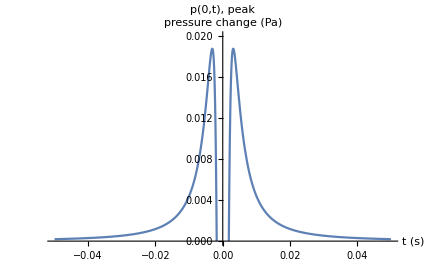

```mathematica
(* 1d *)
Plot[p[0,t],{t,-15,15},PlotRange->{0,4(10^-6)},PlotLabel->"p(0,t)",AxesLabel->{"t (s)","pressure change (Pa)"}]
Plot[p[0,t],{t,-0.05,0.05},PlotRange->{4(10^-6),2(10^-2)},PlotLabel->"p(0,t), peak",AxesLabel->{"t (s)","pressure change (Pa)"}]
```

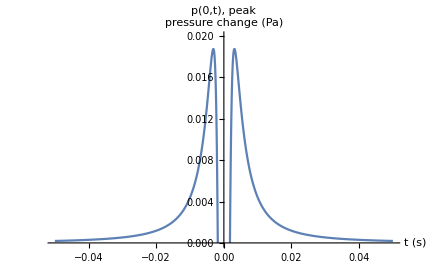

-Graphics-